## Part 1: Plotting a Least Squares Solution for Financial Data

Least squares line coefficients:

{-0.000838159,22.7467}

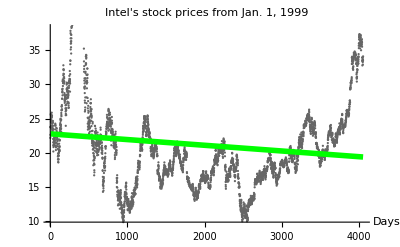

```mathematica
fdata = FinancialData["INTC", "Jan. 1, 1999"]; (* loading financial data with respect to Intel *)
(* DateListPlot[fdata] *)

(* create the data and solve least squares, from LSQline.nb *)
length=Length[fdata];
data=Table[fdata[[i,2]],{i,1,length}];
datplot=ListPlot[data,PlotStyle->{GrayLevel[0.4],PointSize[0.004]}, PlotLabel->Style["Intel's stock prices from Jan. 1, 1999", FontSize->18, FontColor->Blue], AxesLabel->{"Days"}];
mat=Table[{i,1},{i,1,length}];
Print["Least squares line coefficients:"];
coeffs=LinearSolve[Transpose[mat].mat,Transpose[mat].data]

(* the least squares line, from LSQline.nb *)
line[x_]:=coeffs[[1]]*x+coeffs[[2]];
lineplot=Plot[line[x],{x,1,length},PlotStyle->{Thickness[0.01], Green}, ImageSize->{672,400},AspectRatio->Full];

Show[{datplot,lineplot}]
```

## Part 2: Compare Uniform versus Chordal Length Parametrizations

SetDelayed::write: Tag Graphics3D in … is Protected.

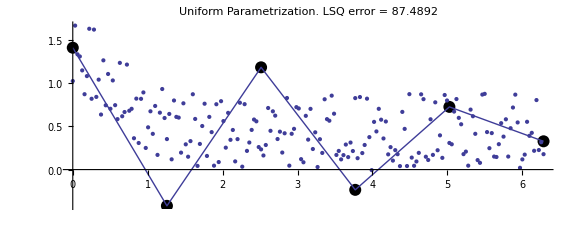

SetDelayed::write: Tag Graphics3D in … is Protected.

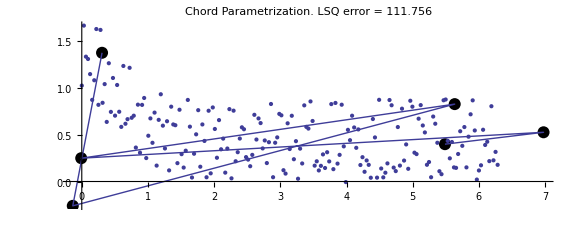

```mathematica
n = 5; (* degree 5 approximate for each parametrization *)
m = 200; (* 200 data points *)
knot = Table[t, {t, 0.0, 1.0, 1/m}]; (* 1/m for uniform set of parameters *)

(* creating the data table and an approximating function, from polynomial_approx.nb *)
data1 = Table[{t, Cos[t]/Exp[t] + 0.9RandomReal[]}, {t, 0.0, 2Pi, (2Pi)/m}];
uniformapprox[n_,knot_,data_]:=
(m=Length[data]-1;
vandermonde=Table[BernsteinBasis[n,j-1,knot[[i]]],{i,1,m+1},{j,1,n+1}];
bez=LinearSolve[Transpose[vandermonde].vandermonde,Transpose[vandermonde].data]; (* bez = LSQ coeffs *)
err = Norm[bez]*Norm[bez]; (* error from LSQ *)
dplot=ListPlot[data];
points=Graphics[{PointSize[0.015],Point[bez]}];
bplot=ListLinePlot[bez];
curve[t_]:=Sum[BernsteinBasis[n,i,t]*bez[[i+1]],{i,0,n}];
cplot=ParametricPlot[curve[t],{t,0,1},PlotStyle->{Thick,Green}];
Show[{cplot,points, bplot, dplot}, ImageSize->Large, PlotRange->All, PlotLabel->Style[SequenceForm["Uniform Parametrization. ", "LSQ error = ", err], FontSize->18, FontColor->Red]]
);
uniformapprox[n, knot, data1]

(* setting up the chordal length parametrization, from interpolation.nb *)
chordknot = knot; 
Do[chordknot[[i+1]] = chordknot[[i]]+Norm[data1[[i+1]]-data1[[i]]], {i, 1, n}];
Do[chordknot[[i]] = chordknot[[i]]/chordknot[[n+1]], {i, 1, n+1}];

chordalapprox[n_,knot_,data_]:=
(m=Length[data]-1;
vandermonde=Table[BernsteinBasis[n,j-1,knot[[i]]],{i,1,m+1},{j,1,n+1}];
bez=LinearSolve[Transpose[vandermonde].vandermonde,Transpose[vandermonde].data];
err = Norm[bez]*Norm[bez]; (* error from LSQ *)
dplot=ListPlot[data];
points=Graphics[{PointSize[0.015],Point[bez]}];
bplot=ListLinePlot[bez];
curve[t_]:=Sum[BernsteinBasis[n,i,t]*bez[[i+1]],{i,0,n}];
cplot=ParametricPlot[curve[t],{t,0,1},PlotStyle->{Thick,Green}];
Show[{cplot,points, bplot, dplot}, ImageSize->Large, PlotRange->All, PlotLabel->Style[SequenceForm["Chord Parametrization. ", "LSQ error = ", err], FontSize->18, FontColor->Red]]
);
chordalapprox[n, chordknot, data1]
```

## Part 3: Creating an Outlier

```mathematica
n = 8; (* degree 8 Bezier Curve *)
m = 100; (* 100 data points *)
knot = Table[t, {t, 0.0, 1.0, 1/m}]; (* 1/m for uniform set of parameters *)

(* creating the data table and an approximating function, from polynomial_approx.nb *)
data1 = Table[{t, Sin[t]+Exp[t]/(Exp[t]-Sin[t]) + 0.9RandomReal[]}, {t, 0.0, 2Pi, (2Pi)/m}];
approx[n_,knot_,data_, p_]:=
(m=Length[data]-1;
vandermonde=Table[BernsteinBasis[n,j-1,knot[[i]]],{i,1,m+1},{j,1,n+1}];
bez=LinearSolve[Transpose[vandermonde].vandermonde,Transpose[vandermonde].data]; (* bez = LSQ coeffs *)
err = Norm[bez]*Norm[bez]; (* error from LSQ *)
dplot=ListPlot[data];
points=Graphics[{PointSize[0.015],Point[bez]}];
bplot=ListLinePlot[bez, PlotStyle->{Pink}];
curve[t_]:=Sum[BernsteinBasis[n,i,t]*bez[[i+1]],{i,0,n}];
cplot=ParametricPlot[curve[t],{t,0,1},PlotStyle->{Thick,Red}];

data1[[50, 2]] = p;   (* change the outlier at this point *)
outlier = Graphics[{PointSize[1.8]}, data1[[50, 2]]];
Show[{cplot,points, bplot, dplot, outlier}, ImageSize->Large, PlotRange->All, PlotLabel->Style[SequenceForm["Outlier Manipulation\n", "LSQ error = ", err], FontSize->18, FontColor->Orange], AspectRatio->1/1]
);

Manipulate[approx[n, knot, data1, p], {{p, -5, "move outlier"}, -15, 15, Appearance->"Labeled"}]
```

SetDelayed::write: Tag Graphics3D in … is Protected.